-Graphics3D-

-Graphics3D-

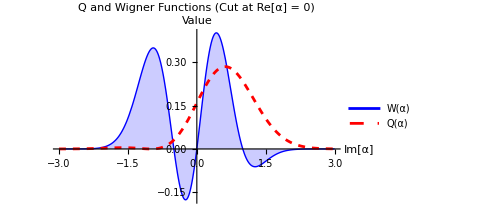

```mathematica
(*Definition of phase space coordinates*)r2[x_,y_]:=x^2+y^2
yCoord[x_,y_]:=y

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for superposition state (|0⟩+i|1⟩)/√2*)
(*Q(α)=1/(2π)*(1+ |α|^2+2 Im[α])*Exp[-|α|^2]*)

QFunction0PlusI1[x_,y_]:=(1/(2*Pi))*(1+r2[x,y]+2*yCoord[x,y])*Exp[-r2[x,y]]

(*--------------------------------------------------------*)
(*2. Wigner function for superposition state (|0⟩+i|1⟩)/√2*)
(*W(α)=2/π*(2|α|^2+2 Im[α] (1-2|α|^2))*Exp[-2|α|^2]*)

WignerFunction0PlusI1[x_,y_]:=(2/Pi)*(2*r2[x,y]+2*yCoord[x,y]*(1-2*r2[x,y]))*Exp[-2*r2[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function*)

Plot3D[QFunction0PlusI1[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"SolarColors",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for State (|0⟩ + i|1⟩)/√2 (Shifted on Im[α] axis)",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function (for displaying negative regions,height range should be properly selected)*)

Plot3D[WignerFunction0PlusI1[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"RustTones",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for State (|0⟩ + i|1⟩)/√2 (Negative region on Im[α] < 0)",Bold,14,Red],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice for clarity of asymmetry and negative values (along Im[α] axis)*)

Plot[{WignerFunction0PlusI1[0,y],QFunction0PlusI1[0,y]},{y,-3,3},PlotLabel->Style["Q and Wigner Functions (Cut at Re[α] = 0)",Bold,14],PlotLegends->{"W(α)","Q(α)"},AxesLabel->{"Im[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```